First run the second half of the D4 notebook to find eq then run the following

```mathematica
selectnD[conds_,n_]:=Select[conds,RegionDimension[ImplicitRegion[#,{a′,γ′}]]==n&]
```

```mathematica
seperateOr[conds_]:=If[Head[LogicalExpand[conds]]===Or,List@@LogicalExpand[conds],{LogicalExpand[conds]}]
```

This will take the values in eq, select out just the conditions (column 3) then seperate them in to distinct regions, then seperate them by dimensionality

```mathematica
rules = Table[DeleteCases[Reduce[Simplify[Reduce[Simplify[#,assumptions′]],assumptions′]]&/@seperateOr[e[[3]]],False],{e,eq}];
rules0D = Table[selectnD[r,0],{r,rules}];
rules1D = Table[selectnD[r,1],{r,rules}];
rules2D = Table[selectnD[r,2],{r,rules}];
```

Here are all the zero dim rules (nash equilibria that are just on a point)

```mathematica
rules0D
```

{{γ′==AlgebraicNumber0.119AlgebraicNumber[Root[2025-5940 #1+4356 #1^2-1062 #1^3+60 #1^4+#1^6&,2],{59/160,-1171/2400,637/2400,-17/480,-1/480,-1/2400}]0.11895541459375736&&a′==AlgebraicNumber0.630AlgebraicNumber[Root[2025-5940 #1+4356 #1^2-1062 #1^3+60 #1^4+#1^6&,2],{0,1/3,0,0,0,0}]0.6300756617312404},{a′==Root0.503Root[32-146 #1^2-87 #1^3+152 #1^4+196 #1^5&,2]0.5034096288628259&&γ′==1/6916252(138783288-3 √(7 (351156463431424-5958129102912 Root49.3Root[1475789056-701092 #1^2-4263 #1^3+76 #1^4+#1^5&,2]49.33414362855694-68154041956 (Root49.3Root[1475789056-701092 #1^2-4263 #1^3+76 #1^4+#1^5&,2]49.33414362855694)^2+225248900 (Root49.3Root[1475789056-701092 #1^2-4263 #1^3+76 #1^4+#1^5&,2]49.33414362855694)^3+13811831 (Root49.3Root[1475789056-701092 #1^2-4263 #1^3+76 #1^4+#1^5&,2]49.33414362855694)^4))-180670448 Root0.503Root[32-146 #1^2-87 #1^3+152 #1^4+196 #1^5&,2]0.5034096288628259-340614092 (Root0.503Root[32-146 #1^2-87 #1^3+152 #1^4+196 #1^5&,2]0.5034096288628259)^2+38602592 (Root0.503Root[32-146 #1^2-87 #1^3+152 #1^4+196 #1^5&,2]0.5034096288628259)^3+593488784 (Root0.503Root[32-146 #1^2-87 #1^3+152 #1^4+196 #1^5&,2]0.5034096288628259)^4)},{a′==1/35 (-7+3 √21)&&γ′==(3 (763+83 √21+5 √(14 (257-13 √21))))/(70 (293+63 √21)),a′==Root0.177Root[-16+72 #1+112 #1^2-50 #1^3+7 #1^4&,2]0.1771637734629069&&γ′==(952+√(2 (62328-24164 Root1.24Root[-5488+3528 #1+784 #1^2-50 #1^3+#1^4&,2]1.2401464142403482-856 (Root1.24Root[-5488+3528 #1+784 #1^2-50 #1^3+#1^4&,2]1.2401464142403482)^2+17 (Root1.24Root[-5488+3528 #1+784 #1^2-50 #1^3+#1^4&,2]1.2401464142403482)^3))+28 Root0.177Root[-16+72 #1+112 #1^2-50 #1^3+7 #1^4&,2]0.1771637734629069-301 (Root0.177Root[-16+72 #1+112 #1^2-50 #1^3+7 #1^4&,2]0.1771637734629069)^2+49 (Root0.177Root[-16+72 #1+112 #1^2-50 #1^3+7 #1^4&,2]0.1771637734629069)^3)/2520},{},{a′==1/3 (-8+3 √5+√(151-66 √5))&&γ′==1/60 (23+3 √5-7 √(151-66 √5)-3 √(5 (151-66 √5))),γ′==1/3&&a′==Root0.153Root[4-16 #1-80 #1^2+84 #1^3+9 #1^4&,3]0.15256625830238094},{γ′==AlgebraicNumber0.119AlgebraicNumber[Root[2025-5940 #1+4356 #1^2-1062 #1^3+60 #1^4+#1^6&,2],{59/160,-1171/2400,637/2400,-17/480,-1/480,-1/2400}]0.11895541459375736&&a′==AlgebraicNumber0.630AlgebraicNumber[Root[2025-5940 #1+4356 #1^2-1062 #1^3+60 #1^4+#1^6&,2],{0,1/3,0,0,0,0}]0.6300756617312404},{},{a′==1/3 (-8+3 √5+√(151-66 √5))&&γ′==1/60 (23+3 √5-7 √(151-66 √5)-3 √(5 (151-66 √5))),γ′==1/3&&a′==Root0.153Root[4-16 #1-80 #1^2+84 #1^3+9 #1^4&,3]0.15256625830238094},{a′==1/2&&γ′==1/7}}

This is the same as above, but reduced to an inexact form so they are easier to see.

```mathematica
rules0D//N//Simplify//MatrixForm
```

({γ′==0.118955&&a′==0.630076}
{a′==0.50341&&γ′==0.141495}
{a′==0.192792&&γ′==0.103604,a′==0.177164&&γ′==0.475037}
{}
{a′==0.185799&&γ′==0.0726516,γ′==0.333333&&a′==0.152566}
{γ′==0.118955&&a′==0.630076}
{}
{a′==0.185799&&γ′==0.0726516,γ′==0.333333&&a′==0.152566}
{a′==0.5&&γ′==0.142857})

And here are all the points plotted.

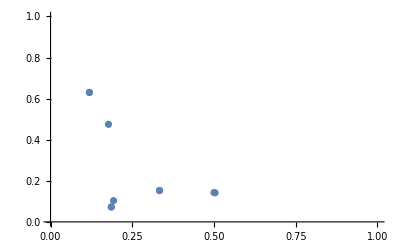

```mathematica
ListPlot[{#[[1,2]],#[[2,2]]}&/@Flatten[rules0D//N],PlotRange->{{0,1},{0,1}}]
```

```mathematica
rules0D//N//MatrixForm
rules1D//N//MatrixForm
```

({γ′==0.118955&&a′==0.630076}
{a′==0.50341&&γ′==0.141495}
{a′==0.192792&&γ′==0.103604,a′==0.177164&&γ′==0.475037}
{}
{a′==0.185799&&γ′==0.0726516,γ′==0.333333&&a′==0.152566}
{γ′==0.118955&&a′==0.630076}
{}
{a′==0.185799&&γ′==0.0726516,γ′==0.333333&&a′==0.152566}
{a′==0.5&&γ′==0.142857})

({}
{}
{}
{γ′≤0.0837078&&a′==-(2. γ′)/(-1.+3. γ′)}
{}
{}
{γ′≤0.0837078&&a′==-(2. γ′)/(-1.+3. γ′)}
{}
{})

```mathematica
OneD = Simplify[Solve[rules1D[[4]],{a′,γ′}],assumptions′]//N
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a′→ConditionalExpression[(2. γ′)/(1.-3. γ′), γ′≤0.0837078]}}